```mathematica
Fiber[seed_,str_,fiber_]:=Module[{newfiber},

If[str == "forward",
If[seed =={}||MemberQ[fiber,seed],
fiber,
If[MemberQ[Surface,seed]&&fiber ≠ {},
Append[fiber,seed]
,
newfiber =Append[fiber,seed];
Fiber[A[seed]["forward"],"forward",newfiber]
]
],

If[seed =={}||MemberQ[fiber,seed],
fiber,
If[MemberQ[Surface,seed]&&fiber ≠ {},
Append[fiber,seed]
,
newfiber =Append[fiber,seed];
Fiber[A[seed]["backward"],"backward",newfiber]
]
]
]
]
```

```mathematica
Block[{$RecursionLimit=10^5},
Fibers = Join[
Table[Fiber[surfacevoxel,"forward",{}],{surfacevoxel,Surface}],
Table[Fiber[surfacevoxel,"backward",{}],{surfacevoxel,Surface}]
];

Fibers=Table[Table[Fibers[[i,j,1;;3]],{j,1,Length[Fibers[[i]]]}],{i,1,Length[Fibers]}];

LongFibers=Select[Fibers,Length[#]>5&];
]
```

```mathematica
Length[Fibers]
```

784

```mathematica
ConnectivityMatrix[]:=Module[{N=Length[SurfacePositions],Connected1 ,Connected2 ,Connected,CM,CleanFibers},

CleanFibers = Select[Fibers,Length[#]>1&];
CM = Table[0,{i,1,N},{j,1,N}];

Table[
Connected1 =Table[If[First[fiber]==voxel && MemberQ[SurfacePositions,Last[fiber]],Last[fiber]],{fiber,CleanFibers}];
Connected2 =Table[If[Last[fiber]==voxel && MemberQ[SurfacePositions,First[fiber]],First[fiber]],{fiber,CleanFibers}];
Connected = Select[Join[Connected1,Connected2],Length[#]>0&];

Table[
CM[[ Position[SurfacePositions,voxel][[1,1]],Position[SurfacePositions,conn][[1,1]] ]] += 1/2;
,{conn,Connected}];

,{voxel,SurfacePositions}];

CM
]
```

```mathematica
CM = ConnectivityMatrix[];
ArrayPlot[CM]
```

-Graphics-

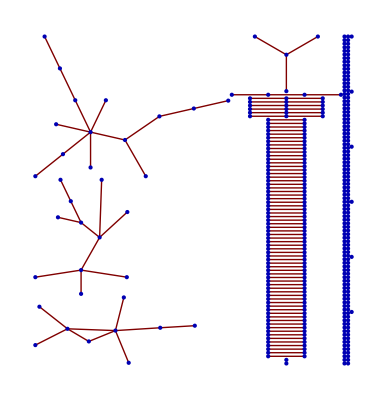

```mathematica
GraphPlot[CM]
```